Second norm of the residual 213.474+46.4603 ⅈ

GreaterEqual::nord: Invalid comparison with 213.474+46.4603 ⅈ attempted.

Time required on the solution 0.172611

1. | -8.53124-7.11387 ⅈ
0.669421 | -11.0518-7.20268 ⅈ
0.404959 | -14.1312-7.27287 ⅈ
0.206612 | -18.05-7.32503 ⅈ
0.0743802 | -22.8997-7.35958 ⅈ
0.00826446 | -20.4845-7.37679 ⅈ
0.00826446 | -20.4845-7.37679 ⅈ
0.0743802 | -22.8997-7.35958 ⅈ
0.206612 | -18.05-7.32503 ⅈ
0.404959 | -14.1312-7.27287 ⅈ
0.669421 | -11.0518-7.20268 ⅈ
1. | -8.53124-7.11387 ⅈ

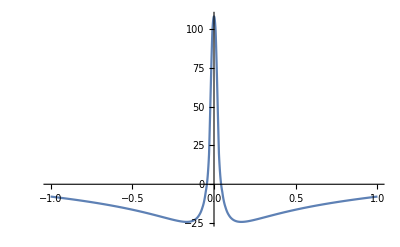

Required time to solve the problem 1.019645

```mathematica
StartTime=AbsoluteTime[];
(*==============================*)
(* Functions and params defentions *)
(*==============================*)

(* Left boundary*)
a=-1;
(* Right boundary*)
b=1;
(*Accurancy of Newton's method*)
eps=10^(-12);
(*Maximum steps for Newton's method*)
MAXITER=100;
(*Kernel*)
K[ξ_,t_,u_]=Sqrt[ξ^2+t^2+u];
(*Rhs function*)
f[t_]=t^2;
DD [ξ_,t_,u_]= D[K[ξ,t,u],u];
(* Number on nodes *)
NN = 100;
(*Grid*)
UniformGrid = Table[i,{i,a,b,(b-a)/(NN-1)}]; 
ff=f[UniformGrid];


(*=======================================*)
(*Filling universal vector α for integrating*)
(*========================================*)
α=Table[0,{NN}];
For[j=1, j<=NN, j++,
(*Preparation for the natural spline making*)
w=Table[{UniformGrid[[i]],0.0},{i,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w];
α[[j]]=Integrate[S[x], {x,a,b}];
]


(*===============================*)
(*========Newton's Algorythm========*)
(*===============================*)

(*Initial condition for solution*)
λ=Table[0.0,{NN}];
(*Zero step to skip algorythm if initial solution is solution of the system*)
Res=Table[ff[[i]]-λ[[i]]+Sum[α[[j]]*K[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]],{j,1,NN}],{i,1,NN}];
Residual=Sqrt[Res.Res];
kk=0;
(*Newton's algorythm*)
While[Residual>=eps ||kk>MAXITER,
(*Matrix Assemble*)
ES=ParallelTable[If[i!=j,
-α[[j]]*DD[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]],
1-α[[j]]*DD[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]]
],{i,1,NN},{j,1,NN}];

(*Find additivies*)
NodesSolution=LinearSolve[ES,Res];
(*New solution vector*)
λ=λ+NodesSolution;
Res=Table[ff[[i]]-λ[[i]]+Sum[α[[j]]*K[UniformGrid[[j]],UniformGrid[[i]],λ[[j]]],{j,1,NN}],{i,1,NN}];
Residual=Sqrt[Res.Res];
Print["Second norm of the residual ", Residual];
kk++;
];

CalculationTime=AbsoluteTime[];
Print["Time required on the solution ", CalculationTime-StartTime];

(*=====================*)
(*Solution visualisation*)
(*=====================*)
SolutionInterpolation=Interpolation[Table[{UniformGrid[[i]],λ[[i]]},{i,1,NN}]];
SolutionAccuracyCheck=Table[{f[t]//N, SolutionInterpolation[t]-NIntegrate[K[x,t,SolutionInterpolation[x]],{x,a,b}]}, {t,a,b,(b-a)/11}];
SolutionAccuracyCheck//TableForm
Plot[SolutionInterpolation[x],{x,a,b},PlotRange->All]
Print["Required time to solve the problem ", AbsoluteTime[]-StartTime];
```